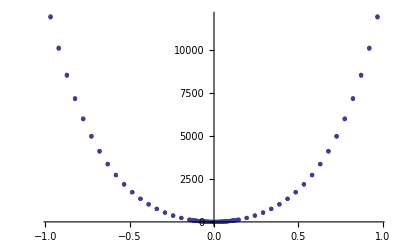

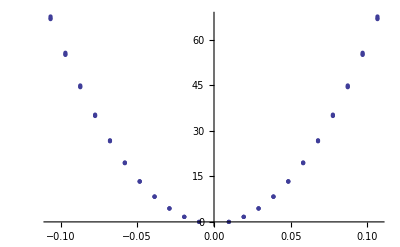

```mathematica
(*Data in*)
SetDirectory["/Volumes/MicroSD/PostDoc_SD/ZrC/Einstein_oscillator_4685Ang_ZrC"];
filesEinsteinPot={"C_300_1900_3200K_energy_displacment","C_300_1900_3200K_energy_displacement_harmonic"};
CarbonPotentialEinstein=ReadList[filesEinsteinPot[[1]],{Number, Number}];
CarbonPotentialEinsteinHarmonic=ReadList[filesEinsteinPot[[2]],{Number, Number}];
Show@ListPlot@CarbonPotentialEinstein
Show@ListPlot@CarbonPotentialEinsteinHarmonic
```

5875.09 x^2

11.006+1.13796×10^-12 x+5379.79 x^2+7746.25 x^4

-0.594182+1.13796×10^-12 x+5890.1 x^2+6025.53 x^4+1337.75 x^6

-0.16809-2.84491×10^-12 x+5858.52 x^2+6221.6 x^4+975.482 x^6+203.15 x^8

-0.622833-2.27593×10^-12 x+5906.28 x^2+5752.54 x^4+2486.22 x^6-1732.02 x^8+854.802 x^10

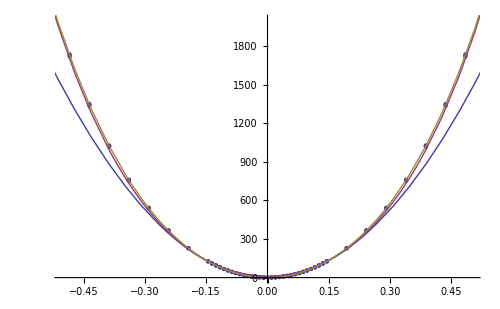

```mathematica
(*Polynomial fit*)
secondOrderFit=Fit[CarbonPotentialEinsteinHarmonic,{x^2},x]
fourthOrderFit=Fit[CarbonPotentialEinstein,{1,x,x^2,x^4},x]
sixthOrderFit=Fit[CarbonPotentialEinstein,{1,x,x^2,x^4,x^6},x]
eigthOrderFit=Fit[CarbonPotentialEinstein,{1,x,x^2,x^4,x^6,x^8},x]
tenthOrderFit=Fit[CarbonPotentialEinstein,{1,x,x^2,x^4,x^6,x^8,x^10},x]
nOrderFit={secondOrderFit,fourthOrderFit,sixthOrderFit,eigthOrderFit};
Show[{ListPlot[CarbonPotentialEinstein,ImageSize->500, PlotRange->{{-0.5,0.5},{0,2000
}}],Plot[{secondOrderFit,fourthOrderFit,sixthOrderFit},{x,-1,1},ImageSize->1200]}]
```

```mathematica
(*Units*)
ℏ=e=m0=1.;ω=1;
```

```mathematica
(*Hamiltonian eigensystem code*)
TISE1D[U_Function,{xmin_,xmax_},N0Grid_: 401,BoundaryCondition_String: "zero"]:=Module[{Δx=(xmax-xmin)/(N0Grid-1),Hmtx,Tmtx,Vmtx},Tmtx=-ℏ.(1/(2.m0.(Δx)^2)) SparseArray[{{i_,i_}->-2,{i_,j_}/;Abs[i-j]==1->1},{N0Grid,N0Grid}];
Vmtx=DiagonalMatrix[U/@Range[xmin,xmax,Δx]];
Hmtx=Tmtx+Vmtx;
If[BoundaryCondition=="periodic",Hmtx[[1,-1]]=Hmtx[[-1,1]]=-ℏ.(1/(2.m0.(Δx)^2)) ;];
Sort[Transpose@Eigensystem[Hmtx],(#1[[1]]<#2[[1]])&]]
```

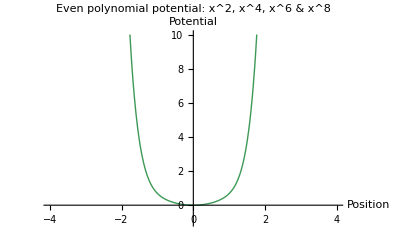

```mathematica
(*Toy symmetric anharmonic Schrodingers in 1d up to 8th order polynomial*)
V[1,x_]=1/2. x^2;
V[2,x_]=1/2. x^2+1/16.x^4;
V[3,x_]=1/2. x^2+1/16.x^4+1/16.x^6;
V4[x_]=1/2. x^2+1/16.x^4+1/16.x^6+1/16.x^8;
Plot[{V1[x],V2[x],V3[x],V4[x]},{x,-4,4}, PlotStyle->Thick,PlotRange->{{-4,4},{-1,10}},PlotLabel->"Even polynomial potential: x^2, x^4, x^6 & x^8",AxesLabel->{"Position","Potential"}]
eigen1=Transpose[TISE1D[Function[{x},V[1,x]],{-10,10},400]][[1,1;;10]]
eigen2=Transpose[TISE1D[Function[{x},V[2,x]],{-10,10},400]][[1,1;;10]]
eigen3=Transpose[TISE1D[Function[{x},V[3,x]],{-10,10},400]][[1,1;;10]]
```

```mathematica
f
```

{0.499921,1.49961,2.49898,3.49804,4.49678,5.49521,6.49332,7.49112,8.4886,9.48577}

{0.539605,1.68432,2.94507,4.29853,5.73081,7.23234,8.79601,10.4163,12.0887,13.8094}

{0.588361,1.9356,3.61214,5.58131,7.80178,10.2454,12.8913,15.7233,18.7281,21.8947}

```mathematica
Hmtx
```

Hmtx

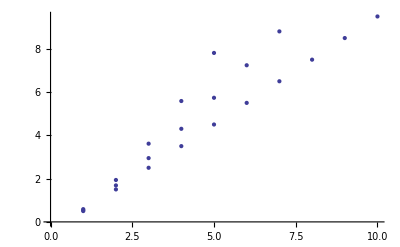

```mathematica
Show[ListPlot[eigen1],ListPlot[eigen2],ListPlot[eigen3]]
eigen[y_]:=Transpose[TISE1D[Function[{x},V[y,x]],{-10,10},400]][[1,1;;10]]
```

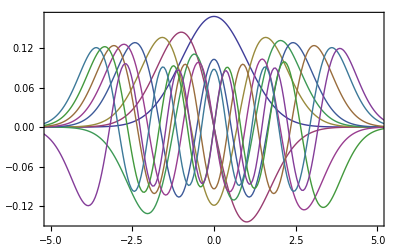

```mathematica
ListPlot[TISE1D[Function[{x},V[1,x]],{-10,10},400][[1;;10,2]],Joined->True,PlotRange->{{-5,5},All},DataRange->{-10,10},Axes->False,Frame->True]
```

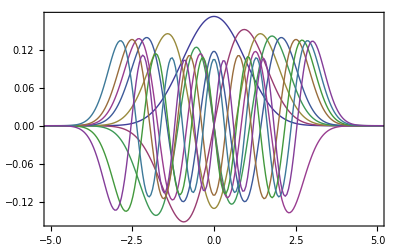

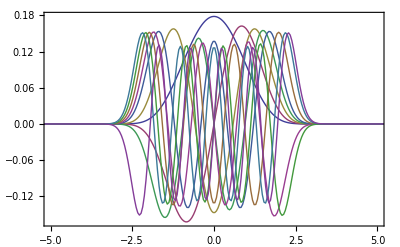

```mathematica
ListPlot[TISE1D[Function[{x},V[2,x]],{-10,10},400][[1;;10,2]],Joined->True,PlotRange->{{-5,5},All},DataRange->{-10,10},Axes->False,Frame->True]
ListPlot[TISE1D[Function[{x},V[3,x]],{-10,10},400][[1;;10,2]],Joined->True,PlotRange->{{-5,5},All},DataRange->{-10,10},Axes->False,Frame->True]
```

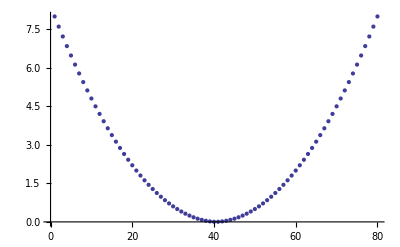

```mathematica
ListPlot[Table[V[1,x/10],{x,1,40}]]
list=Table[V[1,x/10],{x,1,40}];
list2=Join[Reverse[list],list];
ListPlot[list2]
```

```mathematica
eigen1
```

{0.499921,1.49961,2.49898,3.49804,4.49678,5.49521,6.49332,7.49112,8.4886,9.48577}

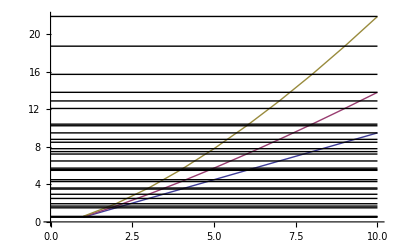

```mathematica
Show[ListPlot[Table[Table[eigen[j][[i]],{i,1,10}],{j,1,3}],Joined->True],Graphics[Table[Table[{Line[{{0,eigen[j][[i]]},{10,eigen[j][[i]]}}]},{i,1,10}],{j,1,3}]]]
```

```mathematica
Table[Table[{Line[{{0,eigen[j][[i]]},{10,eigen[j][[i]]}}]},{i,1,10}],{j,1,3}]
```

{{{Line[{{0,0.499921},{10,0.499921}}]},{Line[{{0,1.49961},{10,1.49961}}]},{Line[{{0,2.49898},{10,2.49898}}]},{Line[{{0,3.49804},{10,3.49804}}]},{Line[{{0,4.49678},{10,4.49678}}]},{Line[{{0,5.49521},{10,5.49521}}]},{Line[{{0,6.49332},{10,6.49332}}]},{Line[{{0,7.49112},{10,7.49112}}]},{Line[{{0,8.4886},{10,8.4886}}]},{Line[{{0,9.48577},{10,9.48577}}]}},{{Line[{{0,0.539605},{10,0.539605}}]},{Line[{{0,1.68432},{10,1.68432}}]},{Line[{{0,2.94507},{10,2.94507}}]},{Line[{{0,4.29853},{10,4.29853}}]},{Line[{{0,5.73081},{10,5.73081}}]},{Line[{{0,7.23234},{10,7.23234}}]},{Line[{{0,8.79601},{10,8.79601}}]},{Line[{{0,10.4163},{10,10.4163}}]},{Line[{{0,12.0887},{10,12.0887}}]},{Line[{{0,13.8094},{10,13.8094}}]}},{{Line[{{0,0.588361},{10,0.588361}}]},{Line[{{0,1.9356},{10,1.9356}}]},{Line[{{0,3.61214},{10,3.61214}}]},{Line[{{0,5.58131},{10,5.58131}}]},{Line[{{0,7.80178},{10,7.80178}}]},{Line[{{0,10.2454},{10,10.2454}}]},{Line[{{0,12.8913},{10,12.8913}}]},{Line[{{0,15.7233},{10,15.7233}}]},{Line[{{0,18.7281},{10,18.7281}}]},{Line[{{0,21.8947},{10,21.8947}}]}}}

```mathematica
Z
```

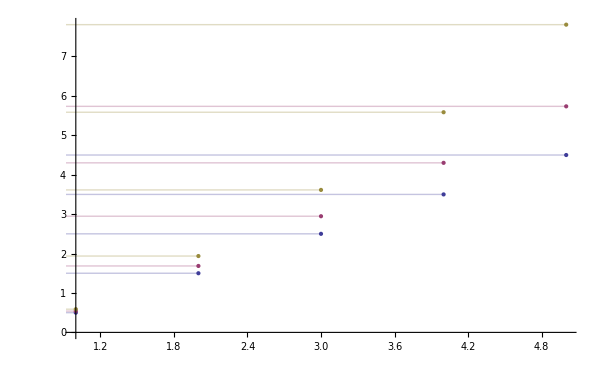

```mathematica
horizontalListPlotFill@ListPlot[Table[Table[{i,eigen[j][[i]]},{i,1,5}],{j,1,3}],PlotStyle->Thick,ImageSize->600]
```